# IGraph/M

## the igraph interface for Mathematica

This notebook can be opened using the command IGDocumentation[] or through the Documentation Center. It cannot be saved, so feel free to re-evaluate cells and experiment.

The documentation is currently incomplete. Contributions are welcome!

## Introduction

IGraph/M provides a Mathematica interface to the popular igraph network analysis package, as well as many other utility functions for working with graphs. The purpose of IGraph/M is not to replace Mathematica’s built-in graph theory functionality, but to complement it. Thus the IGraph/M interface is designed to interoperate seamlessly with built-in functions and datatypes, while also being familiar to users of other igraph interfaces (R, Python or C).

Only igraph functionality not already available in Mathematica is exposed. While many of the functions that IGraph/M provides overlap with built-in ones, like IGBetweenness and BetweeneessCentrality, there are usually some relevant differences. For example, IGBetweenness uses edge weights, while BetweennessCentrality does not.

## Basic usage

The package can be loaded using

```mathematica
Needs["IGraphM`"]
```

The list of included functions is below. Notice that their names always have the IG prefix. After loading the package, click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

Or just type a question mark followed by the symbol’s name:

```mathematica
?IGVersion
```

```mathematica
IGVersion[]
```

IGraph/M functions work directly with Mathematica’s built-in Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples. Let us first generate a graph using the built-in functions of Mathematica.

```mathematica
SeedRandom[42];
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex using IGraph/M ...

```mathematica
IGBetweenness[g]
```

... or using Mathematica, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

Notice that Mathematica 11.2 does not include functionality to compute weighted betweenness. The builtin function BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

Let us delete the minimum feedback edge set to obtain an acyclic graph:

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

```mathematica
IGSeedRandom[42];
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

Increasing the number of iterations will usually improve the result.

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. The igraph documentation provides article references for most nontrivial algorithms. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not yet be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, EdgeLabels, VertexStyle, GraphStyle, PlotTheme, etc.

```mathematica
IGLCF[{5,-5},7,GraphStyle->"SmallNetwork"]
```

Many included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

### Deterministic graph generators

#### IGEmptyGraph

```mathematica
?IGEmptyGraph
```

IGEmptyGraph is a convenience function for creating graphs with no edges.

Create a null graph.

```mathematica
IGEmptyGraph[]//VertexCount
```

Create an empty graph on 4 vertices.

```mathematica
IGEmptyGraph[15]
```

#### IGLCF

```mathematica
?IGLCF
```

IGLCF[{k_1,k_2,…},n] creates a graph based on the LCF notation [k_1,k_2,…]^n.

The Möbius–Kantor graph is [5,-5]^8.

```mathematica
IGLCF[{5,-5},8,GraphStyle->"DiagramGreen"]
```

The Pappus graph is [5,7,-7,7,-7,-5]^3.

```mathematica
IGLCF[{5,7,-7,7,-7,-5},3,GraphStyle->"ThickEdge"]
```

The cuboctahedral graph is [4,2]^6.

```mathematica
IGLayoutKamadaKawai3D@IGLCF[{4,2},6]
```

#### IGGraphAtlas

```mathematica
?IGGraphAtlas
```

```mathematica
IGGraphAtlas[789]
```

#### IGMakeLattice

```mathematica
?IGMakeLattice
```

IGMakeLattice[{d_1,d_2,…}] creates a lattice graph of the given dimensions. The available options are:

"Radius" controls the size of the neighbourhood within which vertices will be connected.

"Periodic"→True creates a periodic lattice.

"Mutual"→True inserts directed edges in both directions when DirectedEdges→True is used.

```mathematica
IGMakeLattice[{3,4},GraphStyle->"VintageDiagram"]
```

```mathematica
IGMakeLattice[{10,10},"Periodic"->True]
```

```mathematica
Graph3D@IGMakeLattice[{5,4,3},GraphStyle->"Prototype"]
```

```mathematica
Graph3D@IGMakeLattice[{2,5},DirectedEdges->True,"Periodic"->True,PlotTheme->"NeonColor"]
```

#### IGKautzGraph

```mathematica
?IGKautzGraph
```

```mathematica
Graph3D@IGKautzGraph[2,2]
```

```mathematica
labels=StringJoin/@DeleteCases[Tuples[{"A","B","C"},{2}],{c_,c_}];
IGKautzGraph[2,1,
VertexLabels->Thread[Range[6]->(Placed[#,Center]&)/@labels],
VertexSize->Large,VertexShapeFunction->"Capsule",PerformanceGoal->"Quality",
PlotTheme->"CoolColor",VertexLabelStyle->White
]
```

#### IGKaryTree

```mathematica
?IGKaryTree
```

The available options are:

DirectedEdges→True creates a directed tree.

```mathematica
IGKaryTree[15]
```

```mathematica
IGKaryTree[10,3,DirectedEdges->True]
```

#### IGCompleteGraph

```mathematica
?IGCompleteGraph
```

The available options are:

DirectedEdges→True creates a directed graph.

SelfLoops→True includes self loops.

```mathematica
IGCompleteGraph[5,SelfLoops->True]
```

#### IGCompleteAcyclicGraph

```mathematica
?IGCompleteAcyclicGraph
```

```mathematica
IGCompleteAcyclicGraph[6]
```

#### IGDeBruijnGraph

```mathematica
?IGDeBruijnGraph
```

```mathematica
IGDeBruijnGraph[3,2,GraphStyle->"BackgroundBlue",EdgeStyle->Thick]
```

#### IGChordalRing

```mathematica
?IGChordalRing
```

```mathematica
IGChordalRing[15,{{3,12,4},{7,8,11}}]
```

### Random graph generators

These graph creation functions use igraph’s random graph generator, which can be seeded using IGSeedRandom.

```mathematica
?*Game
```

#### IGDegreeSequenceGame

```mathematica
?IGDegreeSequenceGame
```

IGDegreeSequenceGame takes the following values for its Method option:

"Simple" may generate both self-loops and multiple edges.

"SimpleNoMultiple" avoids self-loops and multiple edges, but it does not guarantee uniform sampling from the space of all graphs with the given degree sequence.

"VigerLatapy" can sample undirected, connected simple graphs uniformly and uses Monte-Carlo methods to randomize the graphs. This generator should be favoured if undirected and connected graphs are to be generated and execution time is not a concern. igraph uses the original implementation of Fabien Viger; see http://www-rp.lip6.fr/~latapy/FV/generation.html and the paper cited on it for the details of the algorithm.

#### IGKRegularGame

```mathematica
?IGKRegularGame
```

In a k-regular graph all vertices have degree k.

The available options are:

DirectedEdges→True creates a directed graph.

"MultipleEdges"→True allows the creation of parallel edges.

```mathematica
IGKRegularGame[10,3]
```

Not all parameters are valid:

```mathematica
IGKRegularGame[5,3]
```

There are no graphs with 5 vertices each having degree 3.

```mathematica
IGGraphicalQ[{3,3,3,3,3}]
```

#### IGGrowingGame

```mathematica
?IGGrowingGame
```

IGGrowingGame[n,k] creates a random graph by successively adding vertices to the graph until the vertex count n is reached. At each step, k new edges are added as well.

The available options are:

DirectedEdges→True creates a directed graph.

"Citation"→True connects newly added edges to the newly added vertex.

```mathematica
IGGrowingGame[50,2]
```

With "Citation"→True, the newly added edges are connected to the newly added vertices.

```mathematica
IGGrowingGame[50,1,"Citation"->True]
```

#### IGBarabasiAlbertGame

```mathematica
?IGBarabasiAlbertGame
```

The available options are:

DirectedEdges→False creates an undirected graph.

"TotalDegreeAttraction"→True computes the attachment probability based on the the total degree of existing vertices (i.e. in- and out-degree), not their in-degree.

"StartingGraph"→g will use graph g as the starting point for building the preferential attachment graph. The vertex names of g are ignored and the result always uses positive integers as vertex names.

Available Method option values:

"Bag" works by putting the ids of the vertices into a bag exactly as many times as their (in-)degree, plus once more. Then the required number of cited vertices are drawn from the bag, with replacement. This method might generate multiple edges. It only works if β=1 and a=1.

"PSumTree" uses a partial prefix-sum tree to generate the graph. It does not generate multiple edges and works for any β and a values.

"PSumTreeMultiple" works like "PSumTree" but allowed multiple edges.

```mathematica
IGBarabasiAlbertGame[100,1]
```

Use attachment probability proportional to degree^1.5+1.

```mathematica
IGBarabasiAlbertGame[100,2,{1.5,1}]
```

The "Bag" method may generate parallel edges:

```mathematica
IGBarabasiAlbertGame[100,2,Method->"Bag"]
```

```mathematica
MultigraphQ[%]
```

Create a graph with the given out-degree sequence. The k^th entry in the degree sequence list must be no greater than k.

```mathematica
IGBarabasiAlbertGame[12,{1,2,3,2,1,3,4,5,1,5,2},PlotTheme->"Minimal"]
```

```mathematica
VertexOutDegree[%]
```

Create a preferential attachment graph using a 4-node complete graph as starting point.

```mathematica
IGBarabasiAlbertGame[10,1,"StartingGraph"->CompleteGraph[4]]
```

#### IGWattsStrogatzGame

```mathematica
?IGWattsStrogatzGame
```

The two-argument form produces results equivalent to that of the built-in WattsStrogatzGraphDistribution.

```mathematica
IGWattsStrogatzGame[30,0.05,PlotTheme->"Web"]
```

The extended form allows for multi-dimensional lattices. Create a graph by randomly rewiring a two-dimensional toroidal lattice of 10×10 nodes:

```mathematica
Graph3D@IGWattsStrogatzGame[10,0.01,{2,1}]
```

#### IGStaticFitnessGame

```mathematica
?IGStaticFitnessGame
```

IGStaticFitnessGame generates a random graph by connecting vertices based on their fitness score. The algorithm starts with n vertices and no edges. Two vertices are selected with probabilities proportional to their fitness scores (for directed graphs, a starting vertex is selected based on its out-fitness and an end vertex based on its in-fitness).  If they are not yet connected, and edge is inserted between them. The procedure is repeated until the number of edges reached m.

The available options are:

SelfLoops→True allows the creation of self loops.

"MultipleEdges"→True allows the creation of parallel edges.

```mathematica
IGStaticFitnessGame[30,Range[10]]
```

```mathematica
IGStaticFitnessGame[30,Range[10],Range[10,1,-1]]
```

#### IGStaticPowerLawGame

```mathematica
?IGStaticPowerLawGame
```

This game generates a directed or undirected random graph where the degrees of vertices follow power-law distributions with prescribed exponents. For directed graphs, the exponents of the in- and out-degree distributions may be specified separately.

This function is equivalent to IGStaticFitnessGame with a fitness vector f where f_i=1/(exponent-1).

Note that significant finite size effects may be observed for exponents smaller than 3 in the original formulation of the game. This function removes the finite size effects by default by assuming that the fitness of vertex i is (i+i_0-1)^-α, where i_0 is a constant chosen appropriately to ensure that the maximum degree is less than the square root of the number of edges times the average degree; see the paper of Chung and Lu, and Cho et al for more details.

The available options are:

SelfLoops→True allows the creation of self loops.

"MultipleEdges"→True allows the creation of parallel edges.

"FiniteSizeCorrection"→False disables finite size correction, which is used by default.

References:

Goh K-I, Kahng B, Kim D: Universal behaviour of load distribution in scale-free networks. Phys Rev Lett 87(27):278701, 2001.

Chung F and Lu L: Connected components in a random graph with given degree sequences. Annals of Combinatorics 6, 125-145, 2002.

Cho YS, Kim JS, Park J, Kahng B, Kim D: Percolation transitions in scale-free networks under the Achlioptas process. Phys Rev Lett 103:135702, 2009.

```mathematica
g=IGStaticPowerLawGame[10000,50000,2.5];
```

```mathematica
Histogram[VertexDegree[g],"Log",{"Log","PDF"}]
```

```mathematica
IGStaticPowerLawGame[50,150,3,3]
```

#### IGStochasticBlockModelGame

```mathematica
?IGStochasticBlockModelGame
```

The ratesMatrix argument gives the connection probability between and within blocks (groups of vertices). The blockSizes argument gives the size of each block (vertex group).

The available options are:

SelfLoops→True allows the creation of self loops.

"MultipleEdges"→True allows the creation of parallel edges.

```mathematica
IGStochasticBlockModelGame[({{0.9, 0.1, 0.2}, {0.1, 1, 0.05}, {0.2, 0.05, 0.9}}),{6,7,8}]
```

#### IGForestFireGame

```mathematica
?IGForestFireGame
```

Reference: Jure Leskovec, Jon Kleinberg and Christos Faloutsos. Graphs over time: densification laws, shrinking diameters and possible explanations. KDD ‘05: Proceeding of the eleventh ACM SIGKDD international conference on Knowledge discovery in data mining, 177–187, 2005.

```mathematica
IGForestFireGame[100,0.2,1,2, GraphLayout->{"EdgeLayout"->"HierarchicalEdgeBundling"}]
```

#### IGCallawayTraitsGame

```mathematica
?IGCallawayTraitsGame
```

This function simulates a growing random graph according to the following algorithm:

At each time step, a new vertex is added. Its type is randomly selected according to the type weights. Then k existing pairs of vertices are selected randomly, and each pair attempts to connect. The probability of success for given types of vertices is given by the preference matrix.

The available options are:

DirectedEdges→True creates a directed graph.

```mathematica
IGCallawayTraitsGame[20,2,{1,2,3},({{1, .5, .3}, {.5, .7, .2}, {.3, .2, .1}})]
```

#### IGEstablishmentGame

```mathematica
?IGEstablishmentGame
```

This function simulates a growing random graph according to the following algorithm:

At each time step, a new vertex is added. Its type is randomly selected according to the type weights. It attempts to connect to k existing vertices. The probability of success for given types of vertices is given by the preference matrix.

The available options are:

DirectedEdges→True creates a directed graph.

```mathematica
IGEstablishmentGame[20,3,{2,1,2},({{1, .5, .3}, {.5, .7, .2}, {.3, .2, .1}})]
```

#### Random bipartite graphs

```mathematica
?IGBipartiteGameGNM
```

```mathematica
?IGBipartiteGameGNP
```

```mathematica
IGBipartiteGameGNP[5,5,0.5,VertexLabels->"Name"]
```

## Graph modification

#### IGRewire

```mathematica
?IGRewire
```

Warning: Most graph properties, such as edge weights, will be lost.

The available options are:

SelfLoops→True allows the creation of self loops.

Generate a random network with scale-free degree distribution:

```mathematica
IGRewire[IGBarabasiAlbertGame[200,2,DirectedEdges->False],10000]
```

#### IGRewireEdges

IGRewireEdges randomly rewires each edge of the graph with the given probability.

Warning: Most graph properties, such as edge weights, will be lost.

```mathematica
?IGRewireEdges
```

The available options are:

SelfLoops→True allows the creation of self loops.

"MultipleEdges"→True allows the creation of multiple edges.

Create a random graph with 10 vertices and 20 edges, while allowing for multiple edges:

```mathematica
IGRewireEdges[RandomGraph[{10,20}],1,"MultipleEdges"->True]
```

```mathematica
EdgeCount[%]
```

#### IGVertexContract

IGVertexContract[g, {set1, set2, …}] will simultaneously contract multiple vertex sets into single vertices.

The name of a contracted vertex will be the same as the first element of the corresponding set. Vertex ordering is not retained.

Warning: Most graph properties, such as edge weights, will be lost.

The available options are:

SelfLoops→True keeps any self loops created during contraction.

"MultipleEdges"→True keeps any parallel edges created during contraction.

```mathematica
?IGVertexContract
```

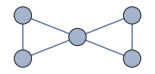
```mathematica
g=-Graphics-;
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},VertexLabels->"Name"]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},SelfLoops->True]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},SelfLoops->True,"MultipleEdges"->True]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},"MultipleEdges"->True]
```

#### IGConnectNeighborhood

IGConnectNeighborhood[g,k] connects each vertex in g to its order k neighbourhood. This operation is also known as the k^th power of the graph.

IGConnectNeighborhood differs from the builtin GraphPower in that it preserves parallel edges and self loops.

Warning: Most graph properties, such as edge weights, will be lost.

```mathematica
?IGConnectNeighborhood
```

Connect each vertex to its second order neighbourhood:

```mathematica
IGConnectNeighborhood[CycleGraph[15]]
```

Connect each vertex to its third order neighbourhood:

```mathematica
IGConnectNeighborhood[GridGraph[{10,10}],3]
```

## Structural properties

### Centrality measures

#### Betweenness

```mathematica
?IGBetweenness
```

```mathematica
?IGBetweennessEstimate
```

```mathematica
?IGEdgeBetweenness
```

```mathematica
?IGEdgeBetweennessEstimate
```

Weighted graphs are supported by all betweenness functions in IGraph/M.

Available Method options for vertex betweenness calculations:

"Precise" is accurate, but slow. This is the default.

"Fast" is fast, but may give incorrect results for large graphs with lots of shortest paths.

```mathematica
g=GridGraph[{30,30}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

For this large grid graph, the "Fast" method no longer gives accurate results:

```mathematica
g=GridGraph[{40,40}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

Possible issues:

Weighted betweenness calculations may be affected by numerical precision when non-integer weights are used. Betweenness computations count shortest path, which means that the total weight of different paths must be compared for equality.  Equality testing with floating point numbers is unreliable.  This can be demonstrated on an example which is purposefully constructed to be problematic.

An unweighted grid graph has many shortest paths between the same pair of vertices.

```mathematica
g=GridGraph[{6,6}];
```

Let us construct non-integer weights which can add up to (equal) integers in many different ways.

```mathematica
weights=1/RandomInteger[{1,5},EdgeCount[g]];
```

Let us now associate weights with edges and order the edges in two different random ways. Betweenness should not depend on edge ordering, so graphs constructed from both should have the same betweenness values.

```mathematica
asc1=Association@RandomSample@Thread[EdgeList[g]->weights];
asc2=Association@RandomSample@Thread[EdgeList[g]->weights];
```

```mathematica
g1=Graph[Keys[asc1],EdgeWeight->Values[asc1]];
g2=Graph[Keys[asc2],EdgeWeight->Values[asc2]];
```

```mathematica
KeySort@AssociationThread[VertexList[g1],IGBetweenness[g1]]-
KeySort@AssociationThread[VertexList[g2],IGBetweenness[g2]]
```

```mathematica
Max@Abs[%]
```

Yet the results differ. This is because IGraph/M works with floating point numbers. Even when different sums of exact weights happen to be equal, floating point calculations will give slightly different results.

To obtain a reliable result, we must use integer weights. The weights in these example were inverses of {1,2,3,4,5}. Multiplying these by their least common multiple will always yield an integer.

```mathematica
LCM@@{1,2,3,4,5}
```

```mathematica
asc1=Association@RandomSample@Thread[EdgeList[g]->60weights];
asc2=Association@RandomSample@Thread[EdgeList[g]->60weights];
```

```mathematica
g1=Graph[Keys[asc1],EdgeWeight->Values[asc1]];
g2=Graph[Keys[asc2],EdgeWeight->Values[asc2]];
```

```mathematica
KeySort@AssociationThread[VertexList[g1],IGBetweenness[g1]]-
KeySort@AssociationThread[VertexList[g2],IGBetweenness[g2]]
```

```mathematica
Chop@Max@Abs[%]
```

Now IGBetweenness gives the same result regardless of edge ordering.

#### Closeness

```mathematica
?IGCloseness
```

```mathematica
?IGClosenessEstimate
```

Weighted graphs are supported.

#### PageRank

```mathematica
?IGPageRank
```

```mathematica
?IGPersonalizedPageRank
```

Weighted graphs and multigraphs are supported.

The default damping factor is 0.85.

The following Method options are available:

"PowerIteration", deprecated, not recommended. Takes suboptions "MaxIterations" and "Epsilon". Does not support weights or multigraphs.

"Arnoldi" uses ARPACK

"PRPACK" uses PRPACK. It is the default method.

#### Eigenvector centrality

```mathematica
?IGEigenvectorCentrality
```

#### Kleinberg’s hub and authority scores

```mathematica
?IGHubScore
```

```mathematica
?IGAuthorityScore
```

#### Burt’s constraint score

```mathematica
?IGConstraintScore
```

### Topological sorting and acyclic graphs

```mathematica
?IGFeedbackArcSet
```

IGFeedbackArcSet[] returns a set of edges the removal of which makes the graph acyclic. With "Exact"→True it finds a minimal feedback arc set. With "Exact"→False it finds a feedback arc set (not necessarily minimal) using the heuristic of Eades, Lin and Smyth (1993).

```mathematica
g=RandomGraph[{10,20},DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
AcyclicGraphQ[%]
```

```mathematica
IGFeedbackArcSet[g]
```

```mathematica
EdgeDelete[g,%]
```

```mathematica
AcyclicGraphQ[%]
```

### Chordal graphs

The maximum cardinality search algorithm visits the vertices of the graph in such an order so that every time the vertex with the most already visited neighbors is visited next. The visiting order is animated below:

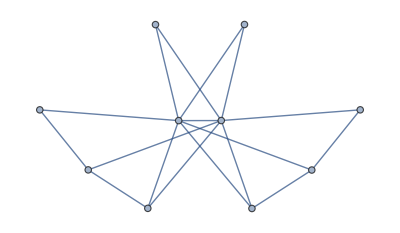
```mathematica
g=-Graphics-;
```

```mathematica
seq=InversePermutation@IGMaximumCardinalitySearch[g]
```

```mathematica
Table[
HighlightGraph[
Graph[g,VertexLabels->"Name"],
Take[seq,-i]
],
{i,1,10}
]//ListAnimate
```

### Clustering coefficient

```mathematica
?IG*ClusteringCoefficient
```

Clustering coefficient calculations ignore edge directions.

IGWeightedClusteringCoefficient computes the weighted local clustering coefficient, as defined by A. Barrat et al. (2004) http://arxiv.org/abs/cond-mat/0311416

### Shortest paths

#### IGDistanceMatrix

```mathematica
?IGDistanceMatrix
```

IGDistanceMatrix takes the following Method options:

Automatic selects a method automatically. As of version 0.3.0, "Unweighted" is selected for unweighted graphs, "Dijkstra" for weighted graphs with only positive weights, and "Johnson" otherwise.

"Unweighted" ignores weights

"Dijkstra" uses Dijkstra’s algorithm. All weights must be non-negative.

"BellmanFord" uses the Bellman–Ford algorithm. Negative weights are supported but all cycles must have a non-negative total weight.

"Johnson" uses the Johnson algorithm. Negative weights are supported but all cycles must have a non-negative total weight.

The igraph C core may override explicit method settings when appropriate. For example, if the graph is not weighted, it always uses "Unweighted".

#### IGDistanceCounts

```mathematica
?IGDistanceCounts
```

IGDistanceCounts[graph] counts all-pair unweighted shortest path lengths in the graph.
IGDistanceCounts[graph, {v_1,v_2,…}] counts unweighted shortest path lengths for paths starting at the given vertices.

For weighted path lengths, or to restrict the computation to both certain start and end vertex sets, use IGDistanceHistogram[].

Compute how the shortest path length distribution changes as we rewire a grid graph k times.

```mathematica
Table[
ListPlot[
Normalize[IGDistanceCounts@IGRewire[GridGraph[{50,50}],k],Total],
Joined->True,Filling->Bottom,PlotLabel->StringTemplate["rewiring steps: ``"][k]
],
{k,{0,5,10,20,50,100}}
]
```

#### IGNeighborhoodSize

```mathematica
?IGNeighborhoodSize
```

#### IGDistanceHistogram

```mathematica
?IGDistanceHistogram
```

IGDistanceHistogram[] computes the weighted shortest path length histogram between the specified start and end vertex sets. The start and end vertex sets do not need to be the same. Note that if the graph is undirected, path lengths between s and t will be double counted (from s→t and t→s) if s and t appear both in the starting and ending vertex sets.

IGDistanceHistogram[] is useful when the result of IGDistanceMatrix[] (or GraphDistanceMatrix[]) does not fit in memory.

#### IGAveragePathLength

```mathematica
?IGAveragePathLength
```

If the graph is unconnected, vertex pairs between which there is no path are excluded from the calculation. This is different from the behaviour of MeanGraphDistance[], which returns ∞ in this case.

#### IGGirth

```mathematica
?IGGirth
```

```mathematica
IGGirth[-Graphics-]
```

#### IGDiameter and IGFindDiameter

```mathematica
?IGDiameter
```

The diameter of a graph is the length of the longest shortest path between any two vertices.

The available options are:

Method can take the values "Unweighted", "Dijkstra" or Automatic. "Dijkstra" takes edge weights into account. Automatic chooses based on whether the graph is weighted.

"ByComponents" controls how unconnected graphs are handled. If False, Infinity is returned. If True, the largest diameter within a component is returned.

```mathematica
IGDiameter[-Graphics-]
```

```mathematica
?IGFindDiameter
```

```mathematica
IGFindDiameter[-Graphics-]
```

```mathematica
g=Entity["Graph","DodecahedralGraph"]["Graph"];
```

```mathematica
HighlightGraph[g,PathGraph@IGFindDiameter[g],
GraphHighlightStyle->"DehighlightFade",PlotTheme->"RoyalColor"
]
```

#### IGEccentricity

```mathematica
?IGEccentricity
```

The eccentricity of a vertex is the longest shortest path to any other vertex. IGEccentricity computes the unweighted eccentricity of each vertex within the connected component where it is contained.

```mathematica
IGEccentricity@CycleGraph[8]
```

#### IGRadius

```mathematica
?IGRadius
```

The radius of a graph is the smallest eccentricity of any of its vertices.

For unconnected graphs, 0 is returned.

### Bipartite graphs

```mathematica
?IGBipartite*
```

#### IGBipartiteQ

```mathematica
?IGBipartiteQ
```

Generate a graph and verify that it is bipartite.

```mathematica
g=IGBipartiteGameGNM[5,5,10,VertexLabels->"Name"]
```

```mathematica
IGBipartiteQ[g]
```

Verify that no edges run between two disjoint vertex subsets of the graph.

```mathematica
IGBipartiteQ[g,{{1,2,3},{6,7,8}}]
```

#### IGBipartitePartitions

```mathematica
?IGBipartitePartitions
```

Find a bipartite partitioning of a graph.

```mathematica
g=-Graphics-;
```

```mathematica
IGBipartitePartitions[g]
```

Ensure that the partitions are returned in such an order that the first one contains vertex 5.

```mathematica
IGBipartitePartitions[g,5]
```

$Failed is returned for non-bipartite graphs.

```mathematica
IGBipartitePartitions[CompleteGraph[4]]
```

#### IGBipartiteProjections

```mathematica
?IGBipartiteProjections
```

The following bipartite graph described the relationship between diseases and genes.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}]
```

```mathematica
parts=Values@GroupBy[
Thread[IGVertexProp["Type"][g]->VertexList[g]],
First->Last
];
```

Construct a disease-disease and gene-gene network from it.

```mathematica
IGBipartiteProjections[g,parts]
```

#### IGBipartiteIncidenceMatrix and IGBipartiteIncidenceGraph

```mathematica
?IGBipartiteIncidenceGraph
```

```mathematica
?IGBipartiteIncidenceMatrix
```

Compute an incidence matrix. The default partitioning used by IGBipartiteIncidenceMatrix is the one returned by IGBipartitePartitions.

```mathematica
g=IGBipartiteGameGNM[5,5,10,VertexLabels->"Name"]
```

```mathematica
bm=IGBipartiteIncidenceMatrix[g];
MatrixForm[bm,TableHeadings->IGBipartitePartitions[g]]
```

Reconstruct a graph from an incidence matrix.

```mathematica
IGBipartiteIncidenceGraph[bm,VertexLabels->"Name",GraphLayout->"BipartiteEmbedding"]
```

Compute an incidence matrix using a given partitioning / vertex ordering. It is allowed to pass only a subset of vertices.

```mathematica
IGBipartiteIncidenceMatrix[g,{{1,2,3},{6,7,8}}]
```

Reconstruct the bipartite graph while specifying vertex names.

```mathematica
IGBipartiteIncidenceGraph[{{a,b,c},{d,e,f}},%,VertexLabels->"Name"]
```

### Similarity measures

```mathematica
?IGBibliographicCoupling
```

```mathematica
?IGCocitationCoupling
```

```mathematica
?IGDiceSimilarity
```

The Dice similarity coefficient of two vertices is twice the number of common neighbors divided by the sum of the degrees of the vertices.

```mathematica
?IGJaccardSimilarity
```

The Jaccard similarity coefficient of two vertices is the number of common neighbors divided by the number of vertices that are neighbors of at least one of the two vertices being considered.

```mathematica
?IGInverseLogWeightedSimilarity
```

The inverse log-weighted similarity of two vertices is the number of their common neighbors, weighted by the inverse logarithm of their degrees. It is based on the assumption that two vertices should be considered more similar if they share a low-degree common neighbor, since high-degree common neighbors are more likely to appear even by pure chance.

Isolated vertices will have zero similarity to any other vertex. Self-similarities are not calculated.

Reference: Lada A. Adamic and Eytan Adar: Friends and neighbors on the Web, Social Networks, 25(3):211-230, 2003.

### Graph components

#### Vertex separators

A vertex separator is a set of vertices whose removal disconnects the graph.

```mathematica
?IGMinimalSeparators
```

```mathematica
?IGMinimumSeparators
```

```mathematica
?IGVertexSeparatorQ
```

```mathematica
?IGMinimalVertexSeparatorQ
```

```mathematica
g=ExampleData[{"NetworkGraph","Friendship"}]
```

```mathematica
separators=IGMinimumSeparators[g]
```

Removing any of these vertex sets will disconnect the graph:

```mathematica
VertexDelete[g,#]&/@separators
```

```mathematica
IGVertexSeparatorQ[g,#]&/@separators
```

```mathematica
IGMinimalVertexSeparatorQ[g,#]&/@separators
```

Removing Anna, Nora and Larry also disconnects the graph, thus this vertex set is a separator:

```mathematica
IGVertexSeparatorQ[g,{"Anna","Nora","Larry"}]
```

But it is not minimal:

```mathematica
IGMinimalVertexSeparatorQ[g,{"Anna","Nora","Larry"}]
```

IGMinimumSeparators returns only those vertex separators which are of the smallest possible size in the graph. IGMinimalSeparators returns all separators which cannot be made smaller by removing a vertex from them. The former is a subset of the latter.

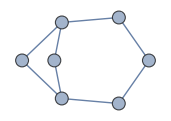
```mathematica
g=-Graphics-;
```

```mathematica
IGMinimalSeparators[g]
```

```mathematica
IGMinimumSeparators[g]
```

```mathematica
SubsetQ[%%,%]
```

#### IGArticulationPoints

IGArticulationPoints finds vertices whose removal increases the number of connected components in the graph. Edge directions are ignored.

```mathematica
?IGArticulationPoints
```

```mathematica
g=Graph[{1->2,2->3,3->1,3->4,4->5,5->6,6->4},DirectedEdges->False,VertexLabels->Automatic]
```

```mathematica
IGArticulationPoints[g]
```

```mathematica
VertexDelete[g,#]&/@%
```

Articulation points are also size-1 separators.

```mathematica
IGMinimumSeparators[g]
```

## Motifs and subgraphs

### Motifs

```mathematica
?IGMotifs
```

IGMotifs counts connected induced subgraphs. As of version 0.3.0, only size 3 and 4 motifs are supported directly. See IGLADSubisomorphismCount to count larger induced subgraphs and IGLADFindSubisomorphisms to find where a certain motif occurs in a graph.

Motif counts are returned ordered by their IGIsoclass. Indeterminate is returned for non-connected subgraphs.

To count non-connected size-3 subgraphs, use IGTriadCensus.

#### Example

Let us find the size-4 motifs that stand out in the E. coli metabolic network by comparing the motif counts to that of a rewired graph:

```mathematica
g=ExampleData[{"NetworkGraph","MetabolicNetworkEscherichiaColi"}];
```

```mathematica
rg=IGRewire[g,50000];
```

```mathematica
ratios=N@Quiet[IGMotifs[g,4]/IGMotifs[rg,4]]
```

```mathematica
largeRatios=Select[ratios,#>5&]
```

There are two motifs that are more than 30 times more common in the metabolic network than in the rewired graph.

```mathematica
Extract[IGData[{"AllDirectedGraphs",4}],FirstPosition[ratios,#]]&/@largeRatios
```

The Davidson–Harel algorithm attempts to reduce edge crossings and can draw these subgraphs in a clearer way:

```mathematica
IGLayoutDavidsonHarel/@%
```

### Triad and dyad census

```mathematica
?IGTriadCensus
```

```mathematica
?IGDyadCensus
```

See IGData["MANTriadLabels"] for the mapping between MAN labels and graphs.

IGTriadCensus[g] does not return triad counts in the same order as IGMotifs[g,3], i.e. ordered according to the triads’ IGIsoclass[]. To get the result ordered by isoclass, use

```mathematica
Lookup[IGTriadCensus[g],Keys@IGData["MANTriadLabels"]]
```

IGData["MANTriadLabels"] are ordered according to isoclass.

### Finding triangles

```mathematica
?IGTriangles
```

```mathematica
?IGAdjacentTriangleCount
```

Label a graph’s vertices based on the number of adjacent triangles.

```mathematica
g=RandomGraph[{8,16},VertexSize->Large];
```

```mathematica
IGVertexMap[Placed[#,Center]&,VertexLabels->IGAdjacentTriangleCount,g]
```

Highlight all triangles in the graph.

```mathematica
HighlightGraph[g,Subgraph[g,#],ImageSize->Tiny,GraphHighlightStyle->"Thick"]&/@IGTriangles[g]
```

## Isomorphism

igraph implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality.

Naming: Most of IGraph/M's isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. Functions named as …GetIsomorphism will find a single isomorphism. Functions named as …FindIsomorphisms can find multiple isomorphisms. Both return a result in a format compatible with the built-in FindGraphIsomorphism.

Additionally, IGIsomorphicQ[] and IGSubisomorphicQ[] try to select the best algorithm for the given graphs. For graphs without multiple edges, they use igraph’s default algorithm selection. For multigraphs, they use VF2 after internally transforming the multigraphs to an edge coloured simple graph.

```mathematica
?IGIsomorphicQ
```

```mathematica
?IGSubisomorphicQ
```

### BLISS

See http://www.tcs.hut.fi/Software/bliss/ and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470920858320 for details. This algorithm is described in the following paper:

T. Junttila, P. Kaski, Engineering an Efficient Canonical Labeling Tool for Large and Sparse Graphs, 2007 Proceedings of the Ninth Workshop on Algorithm Engineering and Experiments, doi:10.1137/1.9781611972870.13.

Bliss generally outperforms Mathematica’s built-in isomorphisms functions (including finding and counting automorphisms) as of Mathematica 11.2. However, this advantage will only be apparent for large and difficult graphs. For small ones the overhead of having to copy the graph and convert it to igraph’s internal format is much larger than the actual computation time.

```mathematica
?IGBliss*
```

All Bliss functions take a "SplittingHeuristics" option, which can influence the performance of the method. Possible values are:

"First" – First non-unit cell. Very fast but may result in large search spaces on difficult graphs. Use for large but easy graphs.

"FirstSmallest" – First smallest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstLargest" – First largest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstMaximallyConnected" – First maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstSmallestMaximallyConnected" – First smallest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstLargestMaximallyConnected" – First largest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

Note: The result of the IGBlissCanonicalLabeling, IGBlissCanonicalPermutation and IGBlissanonicalGraph functions depend on the choice of "SplittingHeuristics". See the Bliss documentation for more information.

#### Basic examples

Let us take the cuboctahedral graph from GraphData …

```mathematica
g1=GraphData["CuboctahedralGraph"]
```

… and also generate it based on its LCF notation.

```mathematica
g2=IGLCF[{4,2},6]
```

The two graphs are isomorphic:

```mathematica
IGBlissIsomorphicQ[g1,g2]
```

One particular mapping between them is the following:

```mathematica
IGBlissGetIsomorphism[g1,g2]
```

How many mappings are there in total? The same number as the number of automorphisms of either graph.

```mathematica
IGBlissAutomorphismCount[g1]
```

Bliss cannot generate all 48 of these mapping directly.  We can either use VF2 for this …

```mathematica
IGVF2FindIsomorphisms[g1,g2]//Length
```

… or we can use the automorphism group computed by Bliss.  The IGBlissAutomorphismGroup[] function will return a generating set of permutations.

```mathematica
generators=IGBlissAutomorphismGroup[g1]
```

We can feed this directly to the built-in function PermutationGroup[]

```mathematica
PermutationGroup[generators]//GroupOrder
```

Ask for all 48 vertex permutations that create isomorphic graphs:

```mathematica
perms=PermutationList[#,VertexCount[g1]]&/@GroupElements@PermutationGroup[generators]
```

Permuting the adjacency matrix with any of these leaves it invariant.

```mathematica
Equal@@(AdjacencyMatrix[g1][[#,#]]&/@perms)
```

Bliss works by computing a canonical labelling of vertices. Then isomorphism can be tested for by comparing the canonically relabelled graphs.

```mathematica
IGBlissCanonicalGraph[g1]===IGBlissCanonicalGraph[g2]
```

IGBlissCanonicalGraph returns graphs in a consistent format so that two graphs are isomorphic if and only if their canonical graphs will compare equal with ===. Note that in Mathematica, graphs may not compare equal

The corresponding permutation and labelling are

```mathematica
IGBlissCanonicalPermutation[g1]
```

```mathematica
IGBlissCanonicalLabeling[g1]
```

Notice that the canonical labelling is simply

```mathematica
AssociationThread[VertexList[g1],IGBlissCanonicalPermutation[g1]]
```

Also notice that it is a mapping from g1 to IGBlissCanonicalGraph[g1]:

```mathematica
MemberQ[
IGVF2FindIsomorphisms[g1,IGBlissCanonicalGraph[g1]],
IGBlissCanonicalLabeling[g1]
]
```

The canonical graph returned by IGBlissCanonicalGraph always has vertices labelled by the integers 1,2,… It can also be used to filter duplicates from a list of graphs

For example, let us generate all possible adjacency matrices of 3-vertex simple directed graphs.

```mathematica
(* fills nondiagonal entries of n by n matrix from vector *)
toMat[vec_,n_]:=SparseArray@Partition[Flatten@Riffle[Partition[vec,n],0,{1,-1,2}],n]
```

There are 2^(3 2)=2^6=64 such matrices.

```mathematica
graphs=AdjacencyGraph[toMat[#,3],DirectedEdges->True]&/@IntegerDigits[Range[2^6]-1,2,6];
```

But only 16 of them correspond to non-isomorphic graphs

```mathematica
DeleteDuplicatesBy[graphs,IGBlissCanonicalGraph]//Length
```

When IGBlissCanonicalGraph is given a vertex coloured graph, it will encode the colours into a vertex property named "Color". This allows distinguishing between graphs whose canonical graphs are identical in structure, but differ in colouring.

Take for example the following coloured graphs:

```mathematica
g=Graph[{1<->2,2<->3},VertexSize->Large,GraphStyle->"BasicBlack"];
colg1=Graph[g,Properties->{1->{"color"->1},2->{"color"->3},3->{"color"->2}}];
colg2=Graph[g,Properties->{1->{"color"->1},2->{"color"->3},3->{"color"->1}}];
```

Visualize them for clarity:

```mathematica
IGVertexMap[ColorData[97],VertexStyle->IGVertexProp["color"]]/@{colg1,colg2}
```

The vertex and edge lists of their canonical graphs are identical:

```mathematica
cang1=IGBlissCanonicalGraph[{colg1,"VertexColors"->"color"}];
cang2=IGBlissCanonicalGraph[{colg2,"VertexColors"->"color"}];
```

```mathematica
VertexList/@{cang1,cang2}
EdgeList/@{cang1,cang2}
```

But they differ in colouring, and therefore do not compare equal:

```mathematica
IGVertexPropertyList[cang1]
```

```mathematica
IGVertexProp["Color"]/@{cang1,cang2}
```

```mathematica
cang1===cang2
```

#### Further examples

Let us visualize the vertex equivalence classes induced by a graph’s automorphism group.

```mathematica
With[{g=GraphData[{"Mycielski", 4}]},HighlightGraph[g,GroupOrbits@PermutationGroup@IGBlissAutomorphismGroup[g],
VertexSize->Large,GraphStyle->"BasicBlack"]
]
```

Visualize the edge equivalence classes of a polyhedron, induced by its graph’s automorphism group.

```mathematica
mesh=PolyhedronData["TruncatedOctahedron","Region"]
```

```mathematica
With[{g=IGMeshGraph[mesh,VertexStyle->Black]},
HighlightGraph[g,
EdgeList[g][[#]]&/@GroupOrbits@PermutationGroup@IGBlissAutomorphismGroup@LineGraph[g]
]
]
```

### VF2

```mathematica
?IGVF2*
```

VF2 supports vertex coloured and edge coloured graphs. A colour specification consists of one of more of the "VertexColors" and "EdgeColors" options. Allowed formats for these options are a list of integers, an association assigning integers to the vertices/edges, or None. When using associations, it is not necessarily to specify a colour for each vertex/edge. The omitted ones are assumed to have colour 0.

#### Examples

The following graph has two automorphisms: {1,2} and {2,1}.

```mathematica
g=Graph[{1<->2}];
IGVF2IsomorphismCount[g,g]
```

If we colour one of the vertices, the permutation {2,1} becomes forbidden, so only one automorphism remains.

```mathematica
IGVF2IsomorphismCount[{g,"VertexColors"->{1,2}},{g,"VertexColors"->{1,2}}]
```

Multigraphs are not directly supported for isomorphism checking, but we can map the multigraph isomorphism problem into an edge-coloured graph isomorphism one by designating the multiplicity of each edge as its colour.

```mathematica
g1=EdgeAdd[PathGraph[Range[5],VertexLabels->"Name"],2<->3]
```

```mathematica
g2=EdgeAdd[PathGraph[Range[5],VertexLabels->"Name"],4<->3]
```

```mathematica
IGVF2IsomorphicQ[g1,g2]
```

Since g1 and g2 are undirected, we need to bring their edges into a sorted canonical form before counting them. This ensures that 4<->3 and 3<->4 are treated as the same edge.

```mathematica
colors1=Counts[Sort/@EdgeList[g1]]
```

```mathematica
colors2=Counts[Sort/@EdgeList[g2]]
```

```mathematica
IGVF2IsomorphicQ[{Graph@Keys[colors1],"EdgeColors"->colors1},{Graph@Keys[colors2],"EdgeColors"->colors2}]
```

IGIsomorphicQ and IGSubisomorphicQ check multigraph isomorphism in a similar way, based on edge colouring.

### LAD

See http://liris.cnrs.fr/csolnon/LAD.html and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470934622128

```mathematica
?IGLAD*
```

With the "Induced"→True option LAD will search for induced subgraphs.



```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-]
```

```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

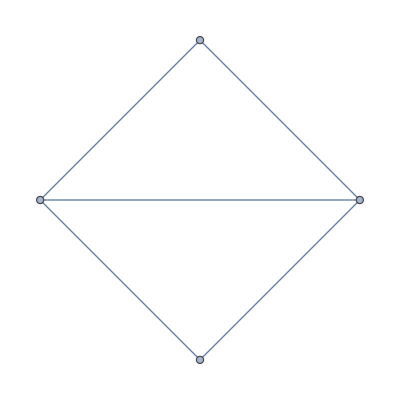
```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

Highlight subgraphs in a grid graph.

```mathematica
g=GridGraph[{3,3}];
HighlightGraph[g,Subgraph[g,#],GraphHighlightStyle->"Thick"]&/@Union[Sort@*Values/@IGLADFindSubisomorphisms[GridGraph[{2,2}],g]]
```

### Coloured graphs

All three included isomorphism algorithms support vertex coloured graphs, and VF2 supports edge coloured graphs as well. A coloured graph is specified as {g, "VertexColors"→…,"EdgeColors"→…}, where both vertex and edge colour specifications are optional. Colours are represented by integers and may be specified in one of the following ways:

A list of integers, given in the same order as VertexList[g] (or EdgeList[g] if specifying edge colours).

{Graph[{a,b},{a<->b}],"VertexColors"→{1,2}}.

An association assigning integers to vertices (or edges). Vertices (or edges) not present in the association are assumed to have colour 0.

{Graph[{a<->b}],"VertexColors"→<|a→1,b→2|>}.

The name of a a vertex (or edge) property. Vertices (or edges) without an assigned property value are assumed to have colour 0.

{Graph[{Property[a,"color"→1],Property[b,"color"→2]},{a<->b}],"VertexColors"→"color"}

"VertexColors"→None indicates no colouring.

Example. Define a graph along with the colours of its vertices.

```mathematica
g=CycleGraph[4];
vcols=<|
1->1,2->1,
3->2,4->2
|>;
```

Visualize it.

```mathematica
Graph[g,
VertexStyle->Normal[ColorData[24]/@vcols],
VertexSize->Medium,VertexLabels->Placed["Name",Center]
]
```

Compute its automorphism group, taking vertex colours into account.

```mathematica
IGBlissAutomorphismGroup[{g,"VertexColors"->vcols}]
```

### Edge and vertex transitivity

#### IGVertexTransitiveQ

```mathematica
?IGVertexTransitiveQ
```

```mathematica
IGVertexTransitiveQ[-Graphics3D-]
```

```mathematica
IGVertexTransitiveQ[-Graphics-]
```

#### IGEdgeTransitiveQ

```mathematica
?IGEdgeTransitiveQ
```

```mathematica
IGEdgeTransitiveQ[-Graphics3D-]
```

```mathematica
IGEdgeTransitiveQ[-Graphics-]
```

The Folkman graph is not vertex transitive but it is edge transitive.

```mathematica
Through[{IGVertexTransitiveQ,IGEdgeTransitiveQ}@GraphData["FolkmanGraph"]]
```

#### IGSymmetricQ

```mathematica
?IGSymmetricQ
```

```mathematica
IGSymmetricQ[GraphData["DodecahedralGraph"]]
```

Make a table of symmetric graphs up to size 7:

```mathematica
Grid[
Table[
Graph[#,ImageSize->50,PlotTheme->"Business"]&/@Select[GraphData/@GraphData[k],IGSymmetricQ],
{k,1,7}
],Frame->All,ItemSize->All]
```

## Maximum flow and connectivity

### Cohesive blocks

The following examples are based on the ones in the R/igraph documentation.

This is the network from the Moody-White paper:

J. Moody and D. R. White. Structural cohesion and embeddedness: A hierarchical concept of social groups. American Sociological Review, 68(1):103–127, Feb 2003.

```mathematica
mw=Graph[{"1"<->"2","1"<->"3","1"<->"4","1"<->"5","1"<->"6","2"<->"3","2"<->"4","2"<->"5","2"<->"7","3"<->"4","3"<->"6","3"<->"7","4"<->"5","4"<->"6","4"<->"7","5"<->"6","5"<->"7","5"<->"21","6"<->"7","7"<->"8","7"<->"11","7"<->"14","7"<->"19","8"<->"9","8"<->"11","8"<->"14","9"<->"10","10"<->"12","10"<->"13","11"<->"12","11"<->"14","12"<->"16","13"<->"16","14"<->"15","15"<->"16","17"<->"18","17"<->"19","17"<->"20","18"<->"20","18"<->"21","19"<->"20","19"<->"22","19"<->"23","20"<->"21","21"<->"22","21"<->"23","22"<->"23"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[mw]
```

```mathematica
CommunityGraphPlot[mw,Rest@blocks,CommunityRegionStyle->Table[Directive[Opacity[0.5],ColorData[96][i]],{i,Length[blocks]-1}]]
```

```mathematica
cohesion
```

Science camp network:

```mathematica
sc=Graph[{"Pauline"<->"Jennie","Pauline"<->"Ann","Jennie"<->"Ann","Jennie"<->"Michael","Michael"<->"Ann","Holly"<->"Jennie","Jennie"<->"Lee","Michael"<->"Lee","Harry"<->"Bert","Harry"<->"Don","Don"<->"Bert","Gery"<->"Russ","Russ"<->"Bert","Michael"<->"John","Gery"<->"John","Russ"<->"John","Holly"<->"Pam","Pam"<->"Carol","Holly"<->"Carol","Holly"<->"Bill","Bill"<->"Pauline","Bill"<->"Michael","Bill"<->"Lee","Harry"<->"Steve","Steve"<->"Don","Steve"<->"Bert","Gery"<->"Steve","Russ"<->"Steve","Pam"<->"Brazey","Brazey"<->"Carol","Pam"<->"Pat","Brazey"<->"Pat","Carol"<->"Pat","Holly"<->"Pat","Gery"<->"Pat"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[sc]
```

```mathematica
CommunityGraphPlot[sc,Rest@blocks,CommunityRegionStyle->ColorData[96],ImageSize->Large]
```

## Cliques and independent vertex sets

```mathematica
?IG*Clique*
```

#### Counting cliques

Mathematica’s FindClique function only finds maximal cliques. IGraph/M provides functions for finding or counting all cliques, i.e. complete subgraphs, of a graph.

```mathematica
g=ExampleData[{"NetworkGraph","CoauthorshipsInNetworkScience"}];
```

```mathematica
{VertexCount[g],EdgeCount[g]}
```

Simply counting cliques is much more memory efficient (and faster) than returning all of them.

```mathematica
IGCliqueSizeCounts[g]
```

```mathematica
BarChart[%,ChartLabels->Range@Length[%]]
```

```mathematica
IGMaximalCliqueSizeCounts[g]
```

```mathematica
BarChart[%,ChartLabels->Range@Length[%]]
```

```mathematica
IGLargestCliques[g]
```

#### Cliques in directed graphs

The clique finder in IGraph/M ignores edge directions.

```mathematica
g=RandomGraph[{10,60},DirectedEdges->True]
```

```mathematica
IGMaximalCliques[g]
```

To find cliques in directed graphs, convert them to undirected and keep reciprocal (bidirectional) edges only.

```mathematica
IGMaximalCliques@IGUndirectedGraph[g,"Reciprocal"]
```

#### Reconstruct bipartite graph of co-occurrence network

```mathematica
g=ExampleData[{"NetworkGraph","LesMiserables"}]
```

```mathematica
ExampleData[{"NetworkGraph","LesMiserables"},"LongDescription"]
```

The maximal cliques of the graph can approximate the scenes in which characters appear together.

```mathematica
cliques=IGMaximalCliques[g];
```

We can construct a bipartite graph of connections between potential scenes and characters

```mathematica
IGLayoutBipartite[
Graph@Catenate[Thread/@Thread[Range@Length[cliques]<->cliques]],
VertexSize->0.5,ImageSize->220
]//IGVertexMap[Placed[#,If[IntegerQ[#],Before,After]]&,VertexLabels->VertexList]
```

## Layout algorithms

The following functions are available:

```mathematica
?IGLayout*
```

If you are looking for the Sugiyama layout from igraph, try the built-in GraphLayout → "LayeredEmbedding", GraphLayout → "LayeredDigraphEmbedding", or LayeredGraphPlot. These are also based on the Sugiyama algorithm.

### Common options and examples

Layout functions also take any standard Graph option.

Many layout algorithms take the following options:

"MaxIterations" controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm and settings. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

"Align"→True aligns the output horizontally. Examples:

```mathematica
{IGLayoutFruchtermanReingold[IGMakeLattice[{2,4}](*, "Align" -> True is the default *)],IGLayoutFruchtermanReingold[IGMakeLattice[{2,4}],"Align"->False]}
```

"Continue" → True allows using existing vertex coordinates as starting points for algorithms that update vertex positions incrementally. We can use this to visualize how the layout algorithms work …

```mathematica
g=IGLayoutRandom@RandomGraph[BarabasiAlbertGraphDistribution[100,1]];
ListAnimate@NestList[IGLayoutGraphOpt[#,"Continue"->True,"MaxIterations"->80]&,g,40]
```

… or to visualize dynamic graph processes such as adding edges to the graph one by one:

```mathematica
g=IGLayoutKamadaKawai@Graph[Range[25],{1<->25},VertexLabels->"Name"];
ListAnimate@NestList[
IGLayoutKamadaKawai[EdgeAdd[#,UndirectedEdge@@RandomSample[VertexList[#],2]],"MaxIterations"->15,"Continue"->True,"Align"->False]&,
g,
30
]
```

Visualize a planar graph without edge crossings using the Davidson–Harel simulated annealing method, and taking starting coordinates from GraphLayout → "PlanarEmbedding".

```mathematica
g=Graph@GraphData[{"Fullerene",{60,1}},"EdgeList"]
```

This layout avoids crossings, but it is not pleasing:

```mathematica
Graph[g,GraphLayout->"PlanarEmbedding"]
```

We can post process it while avoiding the introduction of any edge crossings:

```mathematica
IGLayoutDavidsonHarel[
IGVertexMap[#&,VertexCoordinates->(Rescale@GraphEmbedding[#,"PlanarEmbedding"]&),g],
"Continue"->True,"EdgeCrossingWeight"->1000
]
```

### Weighted graphs

Several of the graph layout algorithms in igraph can take edge weights into accounts. How the weights are used during layout differs between them.

IGLayoutFruchtermanReingold multiplies the attraction between vertices by the weights. Thus higher weights result in shorter edges.

IGLayoutKamadaKawai produces longer edges for higher weights

### Drawing trees

IGLayoutReingoldTilford[] and IGLayoutReingoldTilfordCircular[] are designed for laying out trees. The following options are available:

"RootVertices" allows nodes to be used as the root nodes in the layout. It must be a list, even if there is a single root node. Multiple root nodes are meant to be used with forests.

DirectedEdges→True lays out the graph so that directed edges are pointing form lower levels (near the root) towards higher ones (away from the root).

"Rotation" controls the orientation of the layout. It must be given in radians.

### Drawing bipartite graphs

```mathematica
?IGLayoutBipartite
```

IGLayoutBipartite draws a bipartite graph, attempting to minimize the number of edge crossing using the Sugiyama algorithm.

```mathematica
IGLayoutBipartite[IGBipartiteGameGNP[10,10,0.2],VertexLabels->"Name"]
```

By default, a partitioning is computed automatically.

```mathematica
g=Graph[{1<->2,3<->4},VertexLabels->"Name"];
IGLayoutBipartite[g]
```

The partitioning can also be specified explicitly.

```mathematica
IGLayoutBipartite[g,"BipartitePartitions"->{{2,3},{4,1}}]
```

The available options are:

"Orientation" can be Horizontal or Vertical

"PartitionGap" controls the size of the gap between the two partitions

"VertexGap" controls the minimum size of the gap between vertices in a partition

MaxIterations controls the maximum number of iterations performed during edge crossing minimization.

"BipartitePartitions" can be used to explicitly specify the partitioning of the graph.

### Drawing large graphs

IGLayoutDrL is designed specifically for visualizing large graphs with high clustering. The following image is created using DrL and shows a 36000 node network of collaborations between condensed matter scientists.

-Graphics-

The image was generated using the following code:

```mathematica
lg=ExampleData[{"NetworkGraph","CondensedMatterCollaborations2005"}];
lg=IndexGraph@Subgraph[lg,First@ConnectedComponents[lg]];
c=IGCommunitiesMultilevel[lg]
pts=GraphEmbedding@IGLayoutDrL[lg]; (* this takes a while *)
figure=Graphics[
GraphicsComplex[pts,
{
{White,AbsoluteThickness[0.3],Opacity[0.05],
Line[List@@@EdgeList[lg]]},
{AbsolutePointSize[2],Opacity[0.7],
MapIndexed[
{ColorData[45]@First[#2],Point[#1]}&,
c["Communities"]
]}
}
],
Background->Black
]
```

⇧-⌤ evaluation is disabled in the cell above to avoid running it accidentally. Running the code takes about 2-3 minutes on a modern computer. Copy the code to a new cell to try it.

### Gallery

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[30,1]];
layouts=Graph[#[g],PlotLabel->#]&/@{IGLayoutCircle,IGLayoutDavidsonHarel,IGLayoutDrL,IGLayoutDrL3D,IGLayoutFruchtermanReingold,IGLayoutFruchtermanReingold3D,IGLayoutGEM,IGLayoutGraphOpt,IGLayoutKamadaKawai,IGLayoutKamadaKawai3D,IGLayoutRandom,IGLayoutReingoldTilford,IGLayoutReingoldTilfordCircular,IGLayoutSphere,IGLayoutBipartite};
Grid@Partition[layouts,4,4,{1,1},""]
```

## Community detection

The following functions are available:

```mathematica
?IGCommunities*
```

### Concepts

Modularity is defined for a given partitioning of a graph’s vertices into communities. It is defined as

Q=1/(2m)∑_(i,j) (A_(i,j)-(k_i k_j)/(2m))δ_(c_i,c_j),

where m is the number of edges, A is the adjacency matrix, k_i is the degree of node i, and c_i is the community that node i belongs to. δ_(i,j) is the Kronecker δ symbol. For weighted graphs, A is the weighted adjacency matrix, k_i are the sum of weights of edges incident on node i, and m is the sum of all weights.

Modularity characterizes the tendency of vertices to connect more within their own group than with other groups. For a given partitioning, it can be computed using IGModularity. Community detection functions find a partitioning of the graph which results in high modularity.

### Basic usage and utility functions

Community detection functions return IGClusterData objects.

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}]
```

```mathematica
cl=IGCommunitiesGreedy[g]
```

The data available in the object can be queries using IGClusterData[…]["Properties"]. See the Examples section below for more information.

```mathematica
cl["Properties"]
```

```mathematica
cl["Communities"]
```

```mathematica
CommunityGraphPlot[g,cl["Communities"],ImageSize->Medium]
```

```mathematica
IGModularity[g,cl]
```

#### IGClusterData

```mathematica
?IGClusterData
```

IGClusterData represents a partitioning of a graph into communities. This object cannot be created directly. It is returned by community detection functions. See the Examples section below for more information.

```mathematica
cl=IGCommunitiesLabelPropagation@ExampleData[{"NetworkGraph","FamilyGathering"}]
```

Query the available properties.

```mathematica
cl["Properties"]
```

Retrieve the communities.

```mathematica
cl["Communities"]
```

When the "Modularity" property is available, Max[cl["Modularity"]] gives the modularity of the current partitioning.

```mathematica
Max[cl["Modularity"]]
```

#### IGModularity

```mathematica
?IGModularity
```

IGModularity[graph,communities] is equivalent to GraphAssortativity[graph,communities,"Normalized"→False].

#### IGCompareCommunities

```mathematica
?IGCompareCommunities
```

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}];
```

```mathematica
{cl1,cl2}={IGCommunitiesGreedy[g],IGCommunitiesEdgeBetweenness[g]}
```

```mathematica
IGCompareCommunities[cl1,cl2]
```

### Community detection methods

#### IGCommunitiesEdgeBetweenness

```mathematica
?IGCommunitiesEdgeBetweenness
```

IGCommunitiesEdgeBetweenness[] implements the Girvan–Newman algorithm.

Weighted graphs are supported. Weights are treated as “distances”, i.e. a large weight represents a weak connection.

Available option values:

"ClusterCount", the number of communities to return. Default: Automatic.

Reference:  M. Girvan and M. E. J. Newman: Community structure in social and biological networks, PNAS 99, 7821-7826 (2002).

#### IGCommunitiesFluid

```mathematica
?IGCommunitiesFluid
```

IGCommunitiesFluid[] implements the fluid communities algorithm.

Reference: Ferran Parés, Dario Garcia-Gasulla, Armand Vilalta, Jonatan Moreno, Eduard Ayguadé, Jesús Labarta, Ulises Cortés, Toyotaro Suzumura: Fluid Communities: A Competitive, Scalable and Diverse Community Detection Algorithm, https://arxiv.org/abs/1703.09307

#### IGCommunitiesGreedy

```mathematica
?IGCommunitiesGreedy
```

IGCommunitiesGreedy[] implements greedy optimization of modularity.

Weighted graphs are supported.

Reference: A Clauset, MEJ Newman, C Moore: Finding community structure in very large networks, http://www.arxiv.org/abs/cond-mat/0408187

#### IGCommunitiesInfoMAP

```mathematica
?IGCommunitiesInfoMAP
```

IGCommunitiesInfoMAP[] implements the InfoMAP algorithm.

It supports both edge weights and vertex weights.

The default number of trials is 10.

References:
M. Rosvall and C. T. Bergstrom, Maps of information flow reveal community structure in complex networks, PNAS 105, 1118 (2008)
M. Rosvall, D. Axelsson, and C. T. Bergstrom, The map equation, Eur. Phys. J. Special Topics 178, 13 (2009)

#### IGCommunitiesLabelPropagation

```mathematica
?IGCommunitiesLabelPropagation
```

Weighted graphs are supported.

Reference:  Raghavan, U.N. and Albert, R. and Kumara, S.: Near linear time algorithm to detect community structures in large-scale networks. Phys. Rev. E 76, 036106. (2007).

#### IGCommunitiesLeadingEigenvector

```mathematica
?IGCommunitiesLeadingEigenvector
```

Weighted graphs are supported.

Available option values:

"ClusterCount", the number of communities to return. May return fewer communities than requested. Default: Automatic.

Reference: MEJ Newman: Finding community structure using the eigenvectors of matrices, Phys. Rev. E 74:036104 (2006).

#### IGCommunitiesMultilevel

```mathematica
?IGCommunitiesMultilevel
```

IGCommunitiesMultilevel[] implements the Louvain community detection method.

Weighted graphs are supported.

Reference: VD Blondel, J-L Guillaume, R Lambiotte and E Lefebvre: Fast unfolding of community hierarchies in large networks, J. Stat. Mech. P10008 (2008)

#### IGCommunitiesOptimalModularity

```mathematica
?IGCommunitiesOptimalModularity
```

Finds the clustering that maximizes modularity exactly. This algorithm is very slow.

Weighted graphs are supported.

#### IGCommunitiesSpinGlass

```mathematica
?IGCommunitiesSpinGlass
```

Weighted graphs are supported.

Option values for "Method" are:

"Original" only supports positive edge weights, but doesn’t check that the supplied weights are actually positive.

"Negative" supports negative weights as well.

Automatic selects "Negative" if negative weights are presents and "Original" otherwise.

Option values for "UpdateRule" are: "Simple", "Configuration"

References:

For Method→"Original, see Joerg Reichardt and Stefan Bornholdt: Statistical Mechanics of Community Detection, http://arxiv.org/abs/cond-mat/0603718

For Method→"Negative", see V.A. Traag and Jeroen Bruggeman: Community detection in networks with positive and negative links, http://arxiv.org/abs/0811.2329

#### IGCommunitiesWalktrap

```mathematica
?IGCommunitiesWalktrap
```

IGCommunitiesWalktrap[] finds communities using short random walks, exploiting the fact that random walks tend to stay within the same cluster.

Weighted graphs are supported.

The default number of steps is 4.

Available option values:

"ClusterCount", the number of communities to return. Default: Automatic.

Reference: Pascal Pons, Matthieu Latapy: Computing communities in large networks using random walks, http://arxiv.org/abs/physics/0512106

### Examples

```mathematica
g=ExampleData[{"NetworkGraph","LesMiserables"}]
```

```mathematica
IGEdgeWeightedQ[g]
```

Community detection functions return IGClusterData objects.

```mathematica
cl1=IGCommunitiesEdgeBetweenness[g,"ClusterCount"->7]
cl2=IGCommunitiesWalktrap[g]
```

Various properties of these objects can be queried:

```mathematica
cl1["Communities"]
```

Visualize the detected communities in two different ways:

```mathematica
CommunityGraphPlot[g,cl1["Communities"]]
```

```mathematica
HighlightGraph[g,Subgraph[g,#]&/@cl1["Communities"],GraphHighlightStyle->"DehighlightGray"]
```

The available properties depend on which algorithm was used for community detection. The following are always present:

"Properties" returns all available properties.

"Algorithm" returns the algorithm used for community detection.

"Communities" returns the list of communities.

"Elements" returns the vertices of the graph.

"ElementCount" returns the vertex count of the graph.

These are present for hierarchical clustering methods:

"HierarchicalClusters" returns the clustering in a format compatible with the Hierarchical Clustering standard package. Note: Isolated vertices may not be included.

"Merges" represents the hierarchical clustering as a sequence of element merges. Elements are represented by their integer indices, and higher indices are introduced for the subclusters formed by the merges. This format is similar to the one used by MATLAB and many other tools. Note: Isolated vertices may not be included.

"Tree" gives a binary tree representation of the merges. Note: Isolated vertices may not be included.

Additionally, the following, and other, algorithm-specific properties may be present:

"Modularity" is a list of modularities for each step of the algorithm, or a single-element list containing the modularity corresponding to the returned clustering. What constitutes a step depends on the particular algorithm.

The "RemoveEdges" property is specific to the "EdgeBetweenness" method, and isn’t present for "Walktrap".

```mathematica
cl1["Properties"]
```

```mathematica
cl1["RemovedEdges"]
```

```mathematica
cl2["Properties"]
```

Multiple properties may be retrieved at the same time.

```mathematica
cl2[{"Algorithm","ElementCount"}]
```

Compare the two clusterings:

```mathematica
IGCompareCommunities[cl1,cl2]
```

Visualize the a hierarchical clustering using the Hierarchical Clustering Package.

```mathematica
<<HierarchicalClustering`
```

```mathematica
DendrogramPlot[cl1["HierarchicalClusters"],LeafLabels->(Rotate[#,Pi/2]&),ImageSize->750,AspectRatio->1/2]
```

Hierarchical community structures can also be obtained as a vertex-weighted tree graph.

```mathematica
g=ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
```

```mathematica
cl=IGCommunitiesGreedy[g];
```

```mathematica
clusteringTree=cl["Tree"]
```

```mathematica
{GraphQ[clusteringTree],IGVertexWeightedQ[clusteringTree]}
```

This tree can be supplied as input to Dendrogram.

```mathematica
Dendrogram[clusteringTree,Left]
```

## Graph colouring

```mathematica
?IGVertexColoring
```

```mathematica
?IGEdgeColoring
```

Compute and visualize a vertex and edge colouring of a Mycielski graph.

```mathematica
g=GraphData[{"Mycielski", 4}];
```

```mathematica
Graph[g,VertexSize->1/3,EdgeStyle->Gray]//
IGVertexMap[ColorData[97],VertexStyle->IGVertexColoring]
```

```mathematica
Graph[g,
EdgeStyle->Directive[Opacity[0.75],AbsoluteThickness[6]],
VertexStyle->Black]//
IGEdgeMap[ColorData[106],EdgeStyle->IGEdgeColoring]
```

Compute a checkerboard-like colouring of a three-dimensional grid graph.

```mathematica
IGVertexMap[ColorData[97],VertexStyle->IGVertexColoring,Graph3D@GridGraph[{4,4,4},VertexSize->0.8]]
```

Compute a colouring of a Voronoi mesh.

```mathematica
mesh=VoronoiMesh[RandomReal[1,{20,2}]]
```

```mathematica
col=IGVertexColoring@IGMeshCellAdjacencyGraph[mesh,2]
```

```mathematica
SetProperty[{mesh,{2,All}},MeshCellStyle->ColorData[97]/@col]
```

## Processes on graphs

#### IGRandomWalk

IGRandomWalk[] takes a random walk over a directed or undirected graph.

```mathematica
?IGRandomWalk
```

How much time does a random walker spend on each node of a network?

```mathematica
g=IGBarabasiAlbertGame[50, 2,DirectedEdges->False]
```

```mathematica
counts=Counts@IGRandomWalk[g,First@VertexList[g],10000]/@VertexList[g]
```

The exact answer can be computed as the leading eigenvector of the process’s stochastic matrix:

```mathematica
sm=Transpose[AdjacencyMatrix[g]/VertexDegree[g]];
{{val},{vec}}=Eigensystem[N[sm],1,Method->{"Arnoldi","Criteria"->"RealPart"}];
```

Compare the exact answer with a finite sample:

```mathematica
ListPlot[{vec/Total[vec],counts/Total[counts]},PlotRange->All,PlotLegends->{"exact","sampled"},PlotStyle->PointSize[0.02]]
```

#### IGRandomEdgeWalk and IGRandomEdgeIndexWalk

```mathematica
?IGRandomEdgeWalk
```

```mathematica
?IGRandomEdgeIndexWalk
```

IGRandomEdgeWalk takes a random walk on a graph and returns the list of traversed edges.

```mathematica
g=IGDeBruijnGraph[3,3];
IGRandomEdgeWalk[g,RandomChoice@VertexList[g],20]
```

IGRandomEdgeIndexWalk returns the list of indices of the traversed edges instead. This makes it useful for working with multigraphs, as it allows distinguishing between parallel edges.

As an example application, let us consider the following set of affine transformations:

```mathematica
scale12=ScalingTransform[{1/2,1/2}];
a11=TranslationTransform[{1/4,√3/4}]@*scale12;
a21=RotationTransform[Pi/3]@*scale12;
b21=TranslationTransform[{3/4,√3/4}]@*RotationTransform[-Pi/3]@*scale12;
a12=TranslationTransform[{1/2,0}]@*ScalingTransform[{1/2,-1/2}];
a22=scale12;
```

```mathematica
trafos={a11,a21,b21,a12,a22};
```

Let us visualize them by showing an an initial (black) triangle and its (red) transformation.

```mathematica
tri=Triangle[{{0,0},{1,0},{1/2,√3/2}}];
Graphics[{tri,Red,GeometricTransformation[tri,#]},ImageSize->Tiny]&/@trafos
```

These transformations describe the mutual self-similarity structure of two fractal curves, according to the following directed graph. Each edge of the graph corresponds to a transformation.

```mathematica
graph=Graph[{1->1,2->1,2->1,1->2,2->2},
VertexLabels->Placed["Name",Center],
VertexShape->{1->-Graphics-,2->-Graphics-},PerformanceGoal->"Quality",
VertexSize->1/3,ImageSize->400
]
```

Let us compute a random walk on this graph, and iteratively apply transformations to the point {0,0} according to the traversed edges.

```mathematica
walk=IGRandomEdgeIndexWalk[graph,1,20000];
pts=Rest@FoldList[#2[#1]&,{0.,0.},trafos⟦walk⟧];
```

The resulting list of points will approximate the union of the two fractal curves.

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point[pts]}]
```

The two curves can be separated by filtering points according to which graph vertex the corresponding directed edge targets. For example, if the point was generated by a transformation corresponding to 1->2, it will belong to curve 2.

```mathematica
targets=Last/@EdgeList[graph]
```

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point@Pick[pts,targets⟦walk⟧,1]}]
```

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point@Pick[pts,targets⟦walk⟧,2]}]
```

The technique described here is taken from “Generating self-affine tiles and their boundaries” by Mark McClure.

## Geometrical meshes

#### IGMeshGraph

```mathematica
?IGMeshGraph
```

The available options are:

EdgeWeight sets either the explicit edge weights, or the mesh property to be used as edge weights. The default value is MeshCellMeasure. Use None to obtain an unweighted graph.

The following example demonstrates finding a shortest path on a geometric mesh.

```mathematica
mesh=DiscretizeRegion[RegionDifference[Rectangle[{0,0},{3,3}],Rectangle[{0,1},{2,2}]],MaxCellMeasure->0.02]
```

IGMeshGraph preserves the vertex coordinates, and uses edge lengths as edge weights by default.

```mathematica
g=IGMeshGraph[mesh]
```

Find the corners.

```mathematica
st=First/@Through[
{MinimalBy,MaximalBy}[VertexList[g],Norm@PropertyValue[{g,#},VertexCoordinates]&]
]
```

Highlight the shortest path.

```mathematica
HighlightGraph[g,
PathGraph@FindShortestPath[g,First[st],Last[st]],
Frame->True,FrameTicks->True
]
```

#### IGMeshCellAdjacencyGraph and IGMeshCellAdjacencMatrix

```mathematica
?IGMeshCellAdjacencyGraph
```

```mathematica
?IGMeshCellAdjacencyMatrix
```

Compute the connectivity of mesh vertices (zero-dimensional cells).

```mathematica
mesh=DiscretizeRegion[Disk[],MaxCellMeasure->0.1]
```

```mathematica
IGMeshCellAdjacencyGraph[mesh,0,VertexCoordinates->MeshCoordinates[mesh]]
```

Compute the connectivity of faces (two-dimensional cells).

```mathematica
IGMeshCellAdjacencyGraph[mesh,2]
```

Compute the connectivity of faces and edges.

```mathematica
g=IGMeshCellAdjacencyGraph[mesh,2,1]
```

This is a bipartite graph.

```mathematica
IGBipartiteQ[g]
```

The vertex names are the same as the mesh cell indices (see MeshCellIndex).

```mathematica
VertexList[g]//Short
```

Colour the faces of the mesh.

```mathematica
SetProperty[{mesh,{2,All}},
MeshCellStyle->ColorData[100]/@IGVertexColoring@IGMeshCellAdjacencyGraph[mesh,2]
]
```

The edge-edge connectivity is identical to the line graph of the vertex-vertex connectivity.

```mathematica
IGIsomorphicQ[
LineGraph@IGMeshCellAdjacencyGraph[mesh,0],IGMeshCellAdjacencyGraph[mesh,1]
]
```

Compute the adjacency matrix of the vertex-vertex connectivity.

```mathematica
mesh=DiscretizeRegion[Sphere[],
PrecisionGoal->1.5,MaxCellMeasure->1,ImageSize->Small]
```

```mathematica
MatrixPlot@IGMeshCellAdjacencyMatrix[mesh,0]
```

Compute the adjacency matrix of the edge-face connectivity.

```mathematica
bm=IGMeshCellAdjacencyMatrix[mesh,1,2]
```

```mathematica
MatrixPlot[bm]
```

This is the (non-square) incidence matrix of a bipartite graph. The graph can be reconstructed using IGBipartiteIncidenceGraph.

```mathematica
Graph3D@IGBipartiteIncidenceGraph[bm]
```

## Notes on other functions

### Random number generator

igraph’s random number generator can be seeded using

```mathematica
IGSeedRandom[123]
```

### IGIndexEdgeList

```mathematica
?IGIndexEdgeList
```

```mathematica
IGIndexEdgeList[Graph[{a,b,c},{b<->c,c<->a}]]
```

```mathematica
Developer`PackedArrayQ[%]
```

IGIndexEdgeList[g] is faster than EdgeList[g] and usually much faster than EdgeList@IndexGraph[g].

```mathematica
g=ExampleData[{"NetworkGraph","CondensedMatterCollaborations"}];
```

```mathematica
{First@RepeatedTiming@EdgeList[g],
First@RepeatedTiming@EdgeList@IndexGraph[g],
First@RepeatedTiming@IGIndexEdgeList[g]}
```

```mathematica
List@@@Sort/@EdgeList@IndexGraph[g]===Sort/@IGIndexEdgeList[g]
```

### IGData

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order motif counting functions use.

```mathematica
IGData[]
```

These are all size 3 directed graphs.

```mathematica
IGData[{"AllDirectedGraphs",3}]//Map[Graph[#,ImageSize->Tiny]&]//Row
```

"MANTriadLabels" refers to the mutual, asymmetric, null labelling of triads used by IGTriadCensus[]. Each label is mapped to the corresponding graph, ordered based on their IGIsoclass. This is useful for converting the output of IGTriadCensus[] to a format compatible with IGMotifs[].

```mathematica
g=RandomGraph[{20,50},DirectedEdges->True];
{IGMotifs[g,3],Lookup[IGTriadCensus[g],Keys@IGData["MANTriadLabels"]]}//Grid
```

## Utilities

The IGraphM`Utilities` package contains a few useful functions which are independent of the core igraph library. This package can also be loaded on its own, using Needs["IGraphM`Utilities`"].

```mathematica
?IGraphM`Utilities`*
```

### Structural transformations

#### IGUndirectedGraph

IGUndirectedGraph[g, method] converts a directed graph to an undirected one, using the specified edge conversion method:

"Simple" creates a single undirected edge between connected vertices

"All" creates one undirected edge for each directed one. This may result in multiple edges between the same vertices.

"Reciprocal" creates an edge only between reciprocally connected vertices.

If the graph was already undirected, it will not be changed.

Warning: As of IGraph/M 0.3, IGUndirectedGraph discards graph properties such as edge weights.

```mathematica
g=-Graphics-;
```

```mathematica
IGUndirectedGraph[g,#]&/@{"Simple","All","Reciprocal"}
```

The default method is "Simple":

```mathematica
IGUndirectedGraph[g]
```

Self-loops are preserved by all methods:

```mathematica
IGUndirectedGraph[Graph[{1,2},{1->1,1->2}],#]&/@{"Simple","All","Reciprocal"}
```

#### IGReverseGraph

IGReverseGraph reverses the direction of each edge while preserving the following graph properties: EdgeWeight, EdgeCapacity, EdgeCost, VertexWeight, VertexCapacity. Other properties are discarded.

Undirected graphs are returned unmodified.

As of IGraph/M 0.3.0, IGReverseGraph does not support multigraphs.

#### IGSimpleGraph

IGSimpleGraph removes self loops and multiple edges between the same vertices, as specified in the options.

The available options are:

SelfLoops→True keeps self loops in the graph.

"MultipleEdges"→True keeps parallel edges in the graph.

```mathematica
IGSimpleGraph[-Graphics-,SelfLoops->#1,"MultipleEdges"->#2]&@@@{{True,True},{True,False},{False,True},{False,False}}
```

#### IGDirectedTree

```mathematica
?IGDirectedTree
```

```mathematica
g=KaryTree[10,3,VertexLabels->"Name"]
```

```mathematica
IGDirectedTree[g,1]
```

```mathematica
IGDirectedTree[g,5,GraphLayout->"LayeredDigraphEmbedding"]
```

Once the tree is made directed, it is easy to find its leaf nodes:

```mathematica
IGSinkVertexList[%]
```

### Weighted graphs

#### IGUnweighted

IGUnweighted[g] returns a version of the graph g with edge weights removed.

```mathematica
?IGUnweighted
```

This function is useful for computing graph properties such as betweenness centrality without taking weights into account.

```mathematica
g=ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}];
```

```mathematica
IGBetweenness[g]
```

```mathematica
IGBetweenness@IGUnweighted[g]
```

#### IGWeightedAdjacencyGraph

IGWeightedAdjacencyGraph constructs an edge-weighted graph from a weighted adjacency matrix. By default, 0 elements in the matrix are taken to indicate a lack of connection. An alternative value may be specified to indicate the lack of connections.

IGWeightedAdjacencyGraph takes the same options as WeightedAjdacencyGraph.

```mathematica
?IGWeightedAdjacencyGraph
```

```mathematica
IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}})]
```

The built-in WeightedAdjacencyGraph uses Infinity to indicate the lack of connection. This makes it inconsistent with WeightedAdjacencyMatrix, which uses 0. The purpose of IGWeightedAdjacencyGraph is to be able to easily interoperate with WeightedAdjacencyMatrix, and to easily cycle a weighted graph through an adjacency matrix representation.

```mathematica
wg=RandomGraph[{8,15},EdgeWeight->RandomReal[1,15]]
```

```mathematica
WeightedAdjacencyMatrix[wg]//MatrixForm
```

```mathematica
{IGWeightedAdjacencyGraph@WeightedAdjacencyMatrix[wg],WeightedAdjacencyGraph@WeightedAdjacencyMatrix[wg]}
```

```mathematica
PropertyValue[%,EdgeWeight]
```

IGWeightedAdjacencyGraph[g,Infinity] is equivalent to WeightedAdjacencyGraph[g].

```mathematica
{IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}}),Infinity],WeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}})]}
```

Use DirectedEdges→True to force creating a directed graph even from a symmetric matrix.

```mathematica
IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}}),DirectedEdges->True]
```

#### IGEdgeWeightedQ

```mathematica
?IGEdgeWeightedQ
```

Unlike WeightedGraphQ, IGEdgeWeightedQ does not return True for vertex weighted graphs that have no edge weights.

```mathematica
g=Graph[{1<->2},VertexWeight->{1.2,2.3}];
```

```mathematica
IGEdgeWeightedQ[g]
```

```mathematica
IGEdgeWeightedQ[SetProperty[g,EdgeWeight->{1}]]
```

#### IGVertexWeightedQ

```mathematica
?IGVertexWeightedQ
```

Unlike WeightedGraphQ, IGVertexWeightedQ does not return True for edge weighted graphs that have no vertex weighted.

```mathematica
g=Graph[{1<->2},EdgeWeight->{3.1}];
```

```mathematica
IGVertexWeightedQ[g]
```

```mathematica
IGVertexWeightedQ[SetProperty[g,VertexWeight->{2,1}]]
```

#### IGVertexStrength

IGVertexStrength returns the strength of each vertex, i.e. the total edge weight of edges adjacent to it.

```mathematica
?IGVertex*Strength
```

```mathematica
g=ExampleData[{"NetworkGraph","EurovisionVotes"}];
```

```mathematica
IGVertexStrength[g]
```

In- and out-strength can be calculated separately for directed graphs.

```mathematica
{IGVertexInStrength[g],IGVertexOutStrength[g]}
```

```mathematica
IGVertexInStrength[g]+IGVertexOutStrength[g]==IGVertexStrength[g]
```

Scale vertices by strength:

```mathematica
IGVertexMap[{"Scaled",0.1#}&,VertexSize->(Normalize[IGVertexStrength[#],Max]&),g]
```

### Property handling functions

```mathematica
g=Graph[ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],ImageSize->Medium]
```

```mathematica
?IGVertexPropertyList
```

```mathematica
?IGEdgePropertyList
```

Find what custom edge and vertex properties this graph has:

```mathematica
IGVertexPropertyList[g]
```

```mathematica
IGEdgePropertyList[g]
```

```mathematica
?IGVertexProp
```

```mathematica
?IGEdgeProp
```

Extract the "Group" property of each node:

```mathematica
IGVertexProp["Group"][g]
```

Extract the weight of each edge:

```mathematica
IGEdgeProp[EdgeWeight][g]
```

```mathematica
?IGVertexMap
```

```mathematica
?IGEdgeMap
```

Show the value of the "FullName" custom property in tooltips.

```mathematica
IGVertexMap[#&,Tooltip->IGVertexProp["FullName"],g]
```

#### Styling graphs according to stored or computed properties

```mathematica
g=Graph[ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],ImageSize->Medium];
```

Scale vertices according to degree:

```mathematica
IGVertexMap[0.1#&,VertexSize->VertexDegree,g]
```

Let us colour edges by betweenness and set their thickness based on weight. Betweenness calculations treat high weight values as a “long distance”, thus we invert EdgeWeight before calculating the betweenness. To be able to use the original weights, we save them into a new "weight" property.

Calls to IGEdgeMap or IGVertexMap can be conveniently chained together using their operator form.

```mathematica
g//
IGEdgeMap[ (* save original weight in "weight" property *)
Identity,"weight"->IGEdgeProp[EdgeWeight]
]/*
IGEdgeMap[ (* invert edge weights for betweenness calculation *)
1/#&,EdgeWeight
]/*
IGEdgeMap[ (* thickness by original weight, colour by betweenness based on inverse weight *)
Directive[AbsoluteThickness[9#1],ColorData["Rainbow"][#2]]&,
EdgeStyle->{IGEdgeProp["weight"],Rescale@*EdgeBetweennessCentrality}
]
```

Label a graph with circular layout:

```mathematica
IGVertexMap[
Function[{name,coord},
Placed[
name,
{{.5,.5},-0.8Normalize[coord]+{.5,.5}},
Rotate[#,Mod[ArcTan@@coord,Pi,-Pi/2]]&
]
],
VertexLabels->{VertexList,IGVertexProp[VertexCoordinates]},
IGLayoutCircle[ExampleData[{"NetworkGraph","FamilyGathering"}]]
]
```

Use edge weights as edge labels, and line up labels with edges:

```mathematica
g=RandomGraph[{10,20},EdgeWeight->RandomReal[1,20]];
```

```mathematica
(* returns edge angle for each edge *)
edgeAngle[g_]:=
With[{asc=AssociationThread[VertexList[g],GraphEmbedding[g]]},
ArcTan@@(asc[#1]-asc[#2])&@@@EdgeList[g]
]
```

```mathematica
IGLayoutDavidsonHarel[g]//
IGEdgeMap[
Function[{weight,angle},
Placed[
Style[NumberForm[weight,2],Background->White],
Center,Rotate[#,Mod[angle,Pi,-Pi/2]]&
]
],
EdgeLabels->{IGEdgeProp@EdgeWeight,edgeAngle}
]
```

Colour vertices based on their graph distance form a given vertex:

```mathematica
g=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}];
```

```mathematica
Graph[g,EdgeStyle->LightGray,VertexSize->1,ImageSize->Medium]//
IGVertexMap[
ColorData["Rainbow"],VertexStyle->(Rescale@First@IGDistanceMatrix[#,{"Feather"}]&)
]
```

Colour the vertices of an annotated bipartite disease-gene graph based on whether they represent diseases or genes.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}];
```

There are two types of vertices:

```mathematica
IGVertexProp["Type"][g]//Union
```

```mathematica
IGVertexMap[
<|"Disease"->Red,"Entrez"->Blue|>,
VertexStyle->IGVertexProp["Type"],
g
]
```

#### Style social network by gender

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}]
```

```mathematica
g=IGVertexMap[
Interpreter["GivenName"][#]["Gender"]&,
"gender"->VertexList,
g
];
```

```mathematica
IGVertexMap[
<|Entity["Gender","Male"]->RGBColor[0., 0.749, 1.],Entity["Gender","Female"]->RGBColor[1., 0.388195, 0.278405]|>,
VertexStyle->IGVertexProp["gender"],
Graph[g,EdgeStyle->Gray,VertexSize->Large]
]
```

#### Transform vertex coordinates

Transform the vertex coordinates of a graph to obtain a more pleasing layout:

```mathematica
g=Graph[GraphData[{"Apollonian",5},"EdgeList"],GraphLayout->"PlanarEmbedding"]
```

```mathematica
IGVertexMap[AffineTransform[{{1,1/2},{0,(√3)/2}}],VertexCoordinates,g]
```

Project coordinates from the sphere to the plane using stereographic projection:

```mathematica
g=Graph3D[GraphData["DodecahedralGraph","EdgeList"]]
```

```mathematica
project=
CoordinateTransform[
{"Standard"->"Stereographic",{"Sphere",1}},
Rest@CoordinateTransform["Cartesian"->"Spherical",#]
]&;
```

```mathematica
Graph[
IGVertexMap[project,VertexCoordinates->Standardize@*IGVertexProp[VertexCoordinates],g],
GraphLayout->{"Dimension"->2}
]
```

#### Copy one property into another

Let us import this network:

```mathematica
g=Import["http://networkdata.ics.uci.edu/data/lesmis/lesmis.gml",ImageSize->Large]
```

According to the description, this should be a weighted graph:

```mathematica
Import["http://networkdata.ics.uci.edu/data/lesmis/lesmis.txt"]
```

But as imported by Mathematica, it is not edge-weighted:

```mathematica
IGEdgeWeightedQ[g]
```

This is because the edge weights are imported into the "value" property instead of the standard EdgeWeight:

```mathematica
IGEdgePropertyList[g]
```

Copy the values of one property into another:

```mathematica
g=IGEdgeMap[#&,EdgeWeight->IGEdgeProp["value"],g];
```

Now we have a weighted graph.

```mathematica
IGEdgeWeightedQ[g]
```

### Import and export functions

IGraph/M provides exporters for certain graph formats. Exporting is done using IGExport and IGExportString, which work analogously to the builtin Export and ExportString. The supported export formats are listed in $IGExportFormats:

```mathematica
$IGExportFormats
```

#### GraphML

As of Mathematica 11.2, the built-in Export function produces non-standard GraphML files that cannot be read by some other graph manipulation packages, such as the igraph library itself. IGExport provides a standards compliant implementation.

```mathematica
IGExportString[
ExampleData[{"NetworkGraph","EurovisionVotes"}],
"GraphML"
]//Short[#,15]& (* avoid showing more than 15 lines *)
```

### Other utility functions

#### IGShorthand

```mathematica
?IGShorthand
```

The available options are:

SelfLoops→True keeps self loops in the graph.

"MultipleEdges"→True keeps parallel edges in the graph.

Construct a cycle graph.

```mathematica
IGShorthand["1-2-3-4-1"]
```

Vertex labels are shown by default. They can be turned off using VertexLabels→None.

```mathematica
IGShorthand["1-2-3-1",VertexLabels->None]
```

The interpretation of - as directed or undirected is controlled by the DirectedEdges option.

```mathematica
IGShorthand["1-2-3-1",DirectedEdges->True]
```

Directed edges can be input using ->, <- or <->.

```mathematica
IGShorthand["Jim -> Suzy <- Joe"]
```

<-> is interpreted as a pair of directed edges.

```mathematica
IGShorthand["1<->2->3"]
```

Mixed graphs, containing both directed and undirected edges, are supported. Note that mixed graphs are not allowed as input to most IGraph/M functions.

```mathematica
IGShorthand["1-2<-3"]
```

Disconnected components are separated by commas.

```mathematica
IGShorthand["1, 2-3, 4-5-6"]
```

Groups of vertices can be given using the colon separator. Edges will be connected to each vertex in the group. This makes it easy to specify a complete graph ...

```mathematica
IGShorthand["A:B:C:D:E -- A:B:C:D:E"]
```

... or a complete bipartite graph.

```mathematica
IGLayoutBipartite@IGShorthand["a:b:c - 1:2:3:4"]
```

Vertex names are taken as strings, except when they can be interpreted as an integer.

```mathematica
IGShorthand["xyz - 137"]//VertexList//InputForm
```

Spaces are allowed in vertex names, and edges can be specified using any number of - characters.

```mathematica
IGShorthand["Sophus Lie --- Camille Jordan"]
```

Self-loops and parallel edges are removed by default because these are often created as an undesired by-product of vertex groups. They can be re-enabled using the SelfLoops or "MultipleEdges" options when desired.

```mathematica
IGShorthand["1:2:3 - 1:2:3",SelfLoops->True]
```

```mathematica
IGShorthand["1:2:3 - 1:2:3",SelfLoops->True,"MultipleEdges"->True]
```

```mathematica
IGShorthand["1-2-1-3","MultipleEdges"->True]
```

#### IGNullGraphQ

```mathematica
?IGNullGraphQ
```

IGNullGraphQ returns True only for the null graph, i.e. the graph that has no vertices.

```mathematica
IGNullGraphQ[IGEmptyGraph[]]
```

For graphs that have vertices, but no edges, it returns False.

```mathematica
IGNullGraphQ[IGEmptyGraph[5]]
```

In contrast, the builtin EmptyGraphQ tests if there are no edges:

```mathematica
EmptyGraphQ[IGEmptyGraph[5]]
```

#### IGPartitionsToMembership and IGMembershipToPartitions

```mathematica
?IGPartitionsToMembership
```

```mathematica
?IGMembershipToPartitions
```

A partitioning of a set of elements can be represented in multiple ways. One way is to list the members of each partition. Another is to annotate each element with the index of the partition it belongs to, i.e. construct a “membership vector”. These functions convert between these representations.

IGraph/M generally uses disjoint subsets to represents partitions. Membership vectors are useful when storing the membership information as vertex attributes, or when exchanging data with other interfaces of igraph.

```mathematica
IGPartitionsToMembership[{a,b,c,d},{{a,c},{d,b}}]
```

```mathematica
IGMembershipToPartitions[{a,b,c,d},{1,2,1,2}]
```

The following graph has the type of nodes encoded as a vertex attribute.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}];
IGVertexProp["Type"][g]//Short
```

Let us extract the attribute values as a vector and construct the two vertex partitions.

```mathematica
parts=IGMembershipToPartitions[VertexList[g],IGVertexProp["Type"][g]];
```

Verify that the graph is bipartite according to this partitioning.

```mathematica
IGBipartiteQ[g,parts]
```

Annotate the vertices of a bipartite graph with their computed membership value.

```mathematica
g=IGBipartiteGameGNM[5,6,14,VertexSize->Large];
```

```mathematica
g=IGVertexMap[
#&,
"membership"->IGPartitionsToMembership[VertexList[g]]@*IGBipartitePartitions,
g
];
```

Colour the vertices accordingly.

```mathematica
IGVertexMap[ColorData[100],VertexStyle->IGVertexProp["membership"],g]
```

Visualize a vertex colouring using HighlightGraph.

```mathematica
g=IGMakeLattice[{2,2,2,2},"Periodic"->True]
```

```mathematica
HighlightGraph[
g,IGMembershipToPartitions[VertexList[g],IGVertexColoring[g]],
VertexSize->Medium,GraphHighlightStyle->"DehighlightGray"
]
```

#### IGSourceVertexList and IGSinkVertexList

```mathematica
?IGSourceVertexList
```

```mathematica
?IGSinkVertexList
```

Find and highlight the source and sink vertices of a random acyclic graph.

```mathematica
g=DirectedGraph[RandomGraph[{10,20}],"Acyclic",VertexLabels->"Name",VertexSize->Large,EdgeStyle->Gray]
```

```mathematica
IGSourceVertexList[g]
```

```mathematica
IGSinkVertexList[g]
```

```mathematica
HighlightGraph[g,{IGSourceVertexList[g],IGSinkVertexList[g]}]
```

Directed graphs have neither source nor sink vertices because undirected edges are counted as bidirectional.

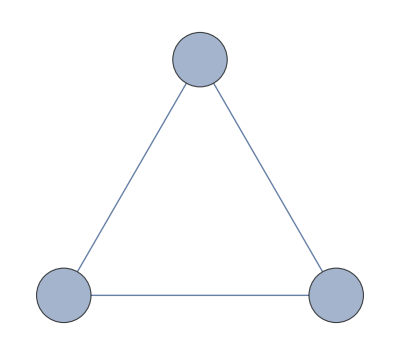
```mathematica
IGSourceVertexList[-Graphics-]
```

These are merely convenience functions that can be implemented straightforwardly as

```mathematica
Pick[VertexList[g],VertexOutDegree[g],0]
```

#### IGReorderVertices

```mathematica
?IGReorderVertices
```

Let us use a styled graph for illustration, to demonstrate that graph properties are preserved.

```mathematica
g1=RandomGraph[{5,5},VertexStyle->{1->Red,3->Green},VertexSize->Medium]
```

```mathematica
g2=IGReorderVertices[{5,4,3,2,1},g1]
```

```mathematica
VertexList/@{g1,g2}
```

```mathematica
IGIsomorphicQ[g1,g2]
```

The result of certain operations, such as DirectedGraph[…,"Acyclic"] or AdjacencyMatrix, depends on the vertex ordering.

```mathematica
DirectedGraph[#,"Acyclic"]&/@{g1,g2}
```

Order the vertices of a directed acyclic graph so that its adjacency matrix is upper triangular.

```mathematica
g=RandomGraph[{10,30},DirectedEdges->True];
g=EdgeDelete[g,IGFeedbackArcSet[g]];
ArrayPlot/@AdjacencyMatrix/@{g,IGReorderVertices[TopologicalSort[g],g]}
```